```mathematica
(2 - (-1)^n) / (Pi * (n^2)*Sqrt[2]) Sin[Sqrt[2]*n*t] * Sin[n*x]
```

((2+(-1)^(1+n)) Sin[√2 n t] Sin[n x])/(√2 n^2 π)

```mathematica
D[((2+(-1)^(1+n)) Sin[√2 n t] Sin[n x])/(√2 n^2 π),{x, 2}]
```

```mathematica
-((2+(-1)^(1+n)) Sin[√2 n t] Sin[n x])/(√2 π)*2
```

-(√2 (2+(-1)^(1+n)) Sin[√2 n t] Sin[n x])/π

```mathematica
D[((2+(-1)^(1+n)) Sin[√2 n t] Sin[n x])/(√2 n^2 π),{t, 2}]
```

-(√2 (2+(-1)^(1+n)) Sin[√2 n t] Sin[n x])/π

```mathematica
f[x_,t_] = D[((2+(-1)^(1+n)) Sin[√2 n t] Sin[n x])/(√2 n^2 π), {t, 1}]
```

((2+(-1)^(1+n)) Cos[√2 n t] Sin[n x])/(n π)

```mathematica
f[x, 0]
```

((2+(-1)^(1+n)) Sin[n x])/(n π)

```mathematica
TrigReduce[((2+(-1)^(1+n)) Sin[n x])/(n π)]
```

-((-2+(-1)^n) Sin[n x])/(n π)

```mathematica
(Sin[x]^3)*Sin[n*x]
```

Sin[x]^3 Sin[n x]

```mathematica
∫Sin[x]^3 Sin[n x]ⅆx
```

1/8 (-Sin[(-3+n) x]/(-3+n)+(3 Sin[(-1+n) x])/(-1+n)-(3 Sin[(1+n) x])/(1+n)+Sin[(3+n) x]/(3+n))

```mathematica
TrigReduce[Sin[x]^3 Sin[n x]]
```

1/8 (3 Cos[x-n x]-Cos[3 x-n x]-3 Cos[x+n x]+Cos[3 x+n x])

```mathematica
∫_0^π 1/8 (3 Cos[x-n x]-Cos[3 x-n x]-3 Cos[x+n x]+Cos[3 x+n x])ⅆx
```

(6 Sin[n π])/(9-10 n^2+n^4)

```mathematica
∫1/8 (3 Cos[x-n x]-Cos[3 x-n x]-3 Cos[x+n x]+Cos[3 x+n x])ⅆx
```

1/8 (-Sin[(-3+n) x]/(-3+n)+(3 Sin[(-1+n) x])/(-1+n)-(3 Sin[(1+n) x])/(1+n)+Sin[(3+n) x]/(3+n))

```mathematica
Sin[x] * Sin[n*x]
```

Sin[x] Sin[n x]

```mathematica
TrigReduce[Sin[x] Sin[n x]]
```

1/2 (Cos[x-n x]-Cos[x+n x])

```mathematica
(Sin[x]^2 )* Sin[n*x]
```

Sin[x]^2 Sin[n x]

```mathematica
∫Sin[x]^2 Sin[n x]ⅆx
```

1/4 (Cos[(-2+n) x]/(-2+n)-(2 Cos[n x])/n+Cos[(2+n) x]/(2+n))

```mathematica
Sin[(1-10)*Pi]
```

0

```mathematica
(Sin[x]^3)*Sin[n*x]
```

Sin[x]^3 Sin[n x]

```mathematica
∫_0^π Sin[x]^3 Sin[n x]ⅆx
```

(6 Sin[n π])/(9-10 n^2+n^4)

```mathematica
(3/4) * Cos[Sqrt[3] * t] * Sin[x] - (1/4)*Cos[3 * Sqrt[3] t ] * Sin[3*x]
```

3/4 Cos[√3 t] Sin[x]-1/4 Cos[3 √3 t] Sin[3 x]

```mathematica
3 *D[3/4 Cos[√3 t] Sin[x]-1/4 Cos[3 √3 t] Sin[3 x], {x, 2}]
```

```mathematica
3 (-3/4 Cos[√3 t] Sin[x]+9/4 Cos[3 √3 t] Sin[3 x])
```

```mathematica
D[3/4 Cos[√3 t] Sin[x]-1/4 Cos[3 √3 t] Sin[3 x], {t, 2}]
```

-9/4 Cos[√3 t] Sin[x]+27/4 Cos[3 √3 t] Sin[3 x]

```mathematica
h[x_,t_] = D[3/4 Cos[√3 t] Sin[x]-1/4 Cos[3 √3 t] Sin[3 x], {t, 1}]
```

-3/4 √3 Sin[√3 t] Sin[x]+3/4 √3 Sin[3 √3 t] Sin[3 x]

```mathematica
h[x, 0]
```

0

```mathematica
x*Sin[n*x]
```

x Sin[n x]

```mathematica
∫_0^π x Sin[n x]ⅆx
```

(-n π Cos[n π]+Sin[n π])/n^2

```mathematica
∫x Sin[n x]ⅆx
```

-(x Cos[n x])/n+Sin[n x]/n^2

```mathematica
((2 * Sin[n * Sqrt[4] * t]) / (n^2 * Sqrt[4]) - (2 * ((-1)^n) * Cos[n*Sqrt[4] * t])/n) * Sin[n*x]
```

(-(2 (-1)^n Cos[2 n t])/n+Sin[2 n t]/n^2) Sin[n x]

```mathematica
D[(-(2 (-1)^n Cos[2 n t])/n+Sin[2 n t]/n^2) Sin[n x], {t, 2}]
```

```mathematica
(8 (-1)^n n Cos[2 n t]-4 Sin[2 n t]) Sin[n x]
4*D[(-(2 (-1)^n Cos[2 n t])/n+Sin[2 n t]/n^2) Sin[n x], {x, 2}]
```

(8 (-1)^n n Cos[2 n t]-4 Sin[2 n t]) Sin[n x]

-4 n^2 (-(2 (-1)^n Cos[2 n t])/n+Sin[2 n t]/n^2) Sin[n x]

```mathematica
ut[x_, t_] = D[(-(2 (-1)^n Cos[2 n t])/n+Sin[2 n t]/n^2) Sin[n x], {t, 1}]
```

```mathematica
D[(-(2 (-1)^n Cos[2 n t])/n+Sin[2 n t]/n^2) Sin[n x], {t,1}]
```

((2 Cos[2 n t])/n+4 (-1)^n Sin[2 n t]) Sin[n x]

```mathematica
x*Sin[n*x]
```

x Sin[n x]

```mathematica
∫_0^π x Sin[n x]ⅆx
```

```mathematica
(-n π Cos[n π]+Sin[n π])/n^2
x(1-x)
```

(-n π Cos[n π]+Sin[n π])/n^2

(1-x) x

```mathematica
Plot[{(1-x) *x,{x,-5.5,6.5}, .25}, PlotRange->{{0, 1} , {0,1}}]
```

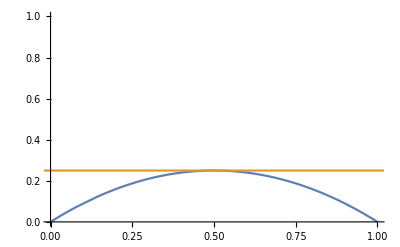

```mathematica
Plot[{(1-x) x, .25},{x,-5.5,6.5},PlotRange->{{0,1},{0,1}}]
```

```mathematica
f[x_,t_,nm_]:=1/6 - 2*Sum[((1 + ((-1)^n))/ ( (n^2)*(Pi^2))) * Cos[n*Pi*t]*Cos[n*Pi*x],{n,1,nm}]
```

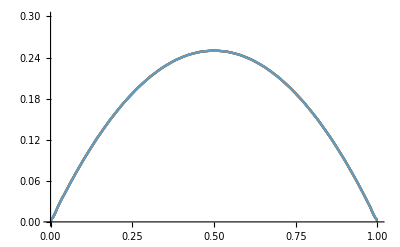

```mathematica
Plot[{x(1-x),Table[f[x,0,50],{t,{0,0.01,0.1,0.5,1,10}}]//Evaluate},{x,0,1}, PlotRange->{{0,1},{0,.3}}]
```

```mathematica
Plot[1/2+Sum[1/(n π) ((-1)^n-1) Sin[n x],{n,1,Infinity}]//Evaluate,{x,-π,π}]
```

```mathematica
Sin[(n*x) / 2]
```

Sin[(n x)/2]

```mathematica
∫_0^π Sin[(n x)/2]ⅆx
```

(4 Sin[(n π)/4]^2)/n

```mathematica
Cos[Pi/2]
```

0

```mathematica
Cos[Pi]
```

-1

```mathematica
Cos[3*Pi/2]
```

0

```mathematica
Cos[4*Pi/2]
```

1

```mathematica
Cos[6*Pi/2]
```

-1

```mathematica
Cos[(3+1/2)*Pi]
```

0

```mathematica
(2/Pi) * ( 1 / (n + 1/2))
```

2/((1/2+n) π)

```mathematica
Simplify[2/((1/2+n) π)]
```

4/(π+2 n π)

```mathematica
Sin[ (n+1/2)*x]
```

Sin[(1/2+n) x]

```mathematica
∫Sin[(1/2+n) x]ⅆx
```

-(2 Cos[(1/2+n) x])/(1+2 n)

```mathematica
z[x_]:=-(2 Cos[(1/2+n) x])/(1+2 n)
```

```mathematica
z[0]
```

-2/(1+2 n)

```mathematica
Cos[Pi*3]
```

-1

```mathematica
Cos[Pi*5]
```

-1

```mathematica
(4)/(Pi*(2*n+1))* Cos[(n+1/2)*t]* Sin[(n+1/2)*x]
```

(4 Cos[(1/2+n) t] Sin[(1/2+n) x])/((1+2 n) π)

```mathematica
x*Cos[n*Pi*x]
```

x Cos[n π x]

```mathematica
∫_0^1 x Cos[n π x]ⅆx
```

(-1+Cos[n π]+n π Sin[n π])/(n^2 π^2)

```mathematica
∫x Cos[n π x]ⅆx
```

Cos[n π x]/(n^2 π^2)+(x Sin[n π x])/(n π)

```mathematica
(x^2)* Cos[n*Pi*x]
```

x^2 Cos[n π x]

```mathematica
∫x^2 Cos[n π x]ⅆx
```

(2 n π x Cos[n π x]+(-2+n^2 π^2 x^2) Sin[n π x])/(n^3 π^3)

```mathematica
Simplify[((x^2) * Sin[n*Pi*x]) / (n*Pi) - 2 /(n*Pi)* (  (-x * Cos[n*Pi*x]) / (n*Pi) + (Sin[n*Pi*x])/((n^2) * Pi^2))]
```

(2 n π x Cos[n π x]+(-2+n^2 π^2 x^2) Sin[n π x])/(n^3 π^3)

```mathematica
x*(1-x) * Cos[n*Pi*x]
```

(1-x) x Cos[n π x]

```mathematica
∫_0^1 (1-x) x Cos[n π x]ⅆx
```

-(n π+n π Cos[n π]-2 Sin[n π])/(n^3 π^3)

```mathematica
Cos[3Pi]
```

-1

```mathematica
1/6 - (1 + (-1)^n) / ( (n^2) * Pi^2) * Cos[n*Pi*x] * Cos[n*Pi*t]
```

1/6-((1+(-1)^n) Cos[n π t] Cos[n π x])/(n^2 π^2)

```mathematica
b[x_, t_] :=Evaluate[D[1/6-((1+(-1)^n) Cos[n π t] Cos[n π x])/(n^2 π^2), {x,1}]]
```

```mathematica
b[0,t]
```

0

```mathematica
b[3,4]
```

((1+(-1)^n) Cos[4 n π] Sin[3 n π])/(n π)

```mathematica
b[2.3, 4.5]
```

((1+(-1)^n) Cos[14.1372 n] Sin[7.22566 n])/(n π)

```mathematica
x*(1-x)
```

(1-x) x

```mathematica
∫_0^1 (1-x) xⅆx
```

1/6

```mathematica
(4 / ((2*n+1) * Pi))*Cos[ (n+1/2)*t]*Sin[(n+1/2)*x]
```

(4 Cos[(1/2+n) t] Sin[(1/2+n) x])/((1+2 n) π)

```mathematica
l[x_,t_]:=(4 Cos[(1/2+n) t] Sin[(1/2+n) x])/((1+2 n) π)
```

```mathematica
l[x,0]
```

(4 Sin[(1/2+n) x])/((1+2 n) π)

```mathematica
Sin[x/2]
```

Sin[x/2]

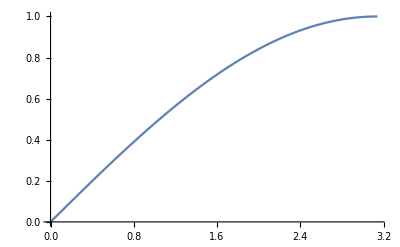

```mathematica
Plot[Sin[x/2],{x,0,Pi}]
```

```mathematica
Exp[Sqrt[x]]
```

ⅇ^(√x)

```mathematica
D[ⅇ^(√x), x]
```

ⅇ^(√x)/(2 √x)

```mathematica
Exp[-Sqrt[x]]
```

ⅇ^(-√x)

```mathematica
D[ⅇ^(-√x), x]
```

-ⅇ^(-√x)/(2 √x)

```mathematica
2/Sqrt[2]
```

√2